```mathematica
Clear["Global`*"];
```

```mathematica
sTot=84614.84435;eTot=3504.020816;
```

```mathematica
sTot=100;eTot=100;
```

```mathematica
dEs={D[x1[t],t]==-k1*x1[t]*x3[t]-k4*x1[t]*x4[t]+k2*x5[t]+k5*x6[t]+k7*x2[t],D[x2[t],t]==k3*x5[t]+k6*x6[t]-k7*x2[t],D[x3[t],t]==-k1*x1[t]*x3[t]+k2*x5[t]+k3*x5[t]-k8*x3[t]+k9*x4[t],D[x4[t],t]==-k4*x1[t]*x4[t]+k5*x6[t]+k6*x6[t]+k8*x3[t]-k9*x4[t],D[x5[t],t]==k1*x1[t]*x3[t]-k2*x5[t]-k3*x5[t]-k10*x5[t]+k11*x6[t],D[x6[t],t]==k4*x1[t]*x4[t]-k5*x6[t]-k6*x6[t]+k10*x5[t]-k11*x6[t]};
```

```mathematica
invaEs={x1[t]+x2[t]+x5[t]+x6[t]==100,x3[t]+x4[t]+x5[t]+x6[t]==100};
```

```mathematica
icEs={x1[0]==sTot,x2[0]==0,x3[0]==eTot,x4[0]==0,x5[0]==0,x6[0]==0};
```

```mathematica
params = {k1->10,k2->0.01,k3->1,k4->0.01,k5->10,k6->100,k7->0.1,k8->100,k9->0.01,k10->0.01,k11->1};
```

```mathematica
solution=NDSolve[{dEs,icEs}/.params,{x1,x2,x3,x4,x5,x6},{t,0,100}];
```

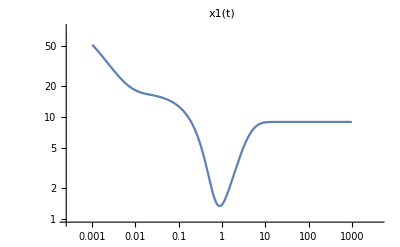
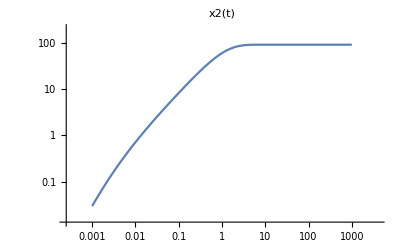
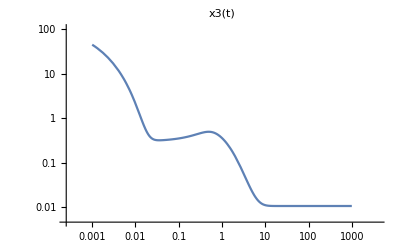
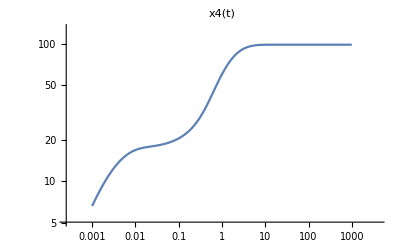
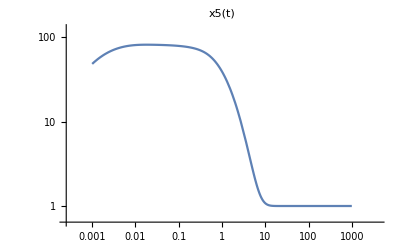
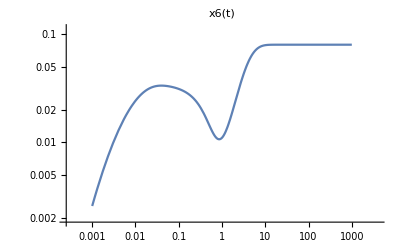

```mathematica
LogLogPlot[Evaluate[#[t]/.solution],{t,10^-3,1000},PlotRange->All,PlotLabel->#[t]]&/@{x1,x2,x3,x4,x5,x6}
```